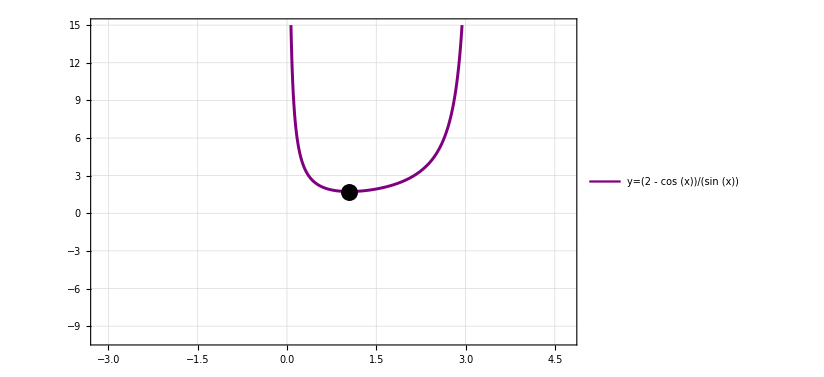

Show[x5]

```mathematica
x4=Plot[(2-Cos[x])/Sin[x],{x,0,π},PlotStyle->{RGBColor["Purple"],Thickness[0.0035]},FrameStyle->Directive[Black,20],Frame->True,FrameLabel->{Style["",30,Black,FontFamily->"Cambria"],Style["",30,Black,FontFamily->"Cambria"]},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],PlotRange->{{-1π,1.5π},{-10,15}},PlotLegends->Placed[LineLegend[{RGBColor["Purple"]},{Style["y=(2 - cos (x))/(sin (x))",20,Black,FontFamily->"Cambria"]}],{0.15,0.8}]];
intersectionPlot=Graphics[{PointSize[0.02],RGBColor["Black"],Point[{π/3,√3}]}];
Show[x4,intersectionPlot]
```